```mathematica
Export["/home/jure/Documents/molecular_simulation/images_md/integrator_accuracy_density09.png", pl]
```

/home/jure/Documents/molecular_simulation/images_md/integrator_accuracy_density09.png

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/jure/Documents/molecular_simulation

```mathematica
getDatap[t_,density_,gamma_,n_ ]:=Block[{data, filename, error, potential, kinetic},
filename=StringJoin[{"md_data_energy_pressure/pressure_density",ToString[NumberForm[density*1.0,{3,2}]], 
"_temperature",ToString[NumberForm[t*1.0,{3,2}]],"_gamma",ToString[NumberForm[gamma*1.0,{3,2}]], "_num_particles", ToString[n], ".dat"}];
data=Import[filename];
Return[data//Flatten];
]
```

```mathematica
p1=getDatap[0.1,0.1,0.4,100];
```

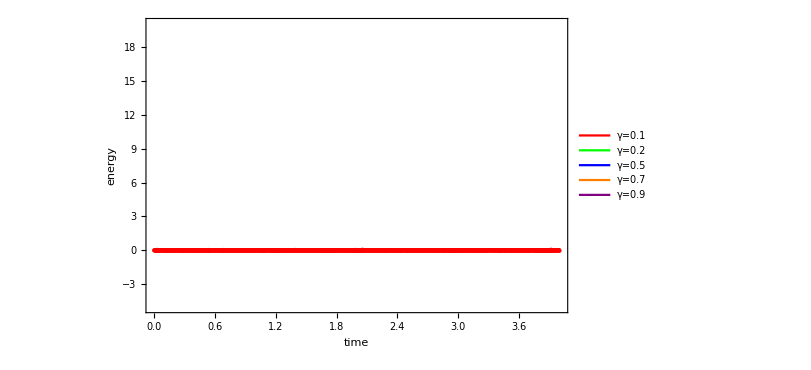

```mathematica
dt=0.002;
pl=ListPlot[{
p1
}
, PlotRange->{-5,20}, Frame->True, ImageSize->600,FrameLabel->{Style["time",20], Style["energy",20]},FrameTicksStyle->14,PlotStyle->{Red,Green,Blue,Orange, RGBColor[{0.5,0,0.5}], Brown, Black},AxesOrigin->{0,0},DataRange->{0.0,dt*Length[p1]},
Epilog->{Inset[LineLegend[{Red,Green,Blue,Orange, RGBColor[{0.5,0,0.5}], Brown, Black},{"γ=0.1", "γ=0.2", "γ=0.5", "γ=0.7","γ=0.9" }, LabelStyle->18, LegendLayout->{"Row",2}],{65,600}],
Inset[Style["T = 0.85", 18],{62,-312}]
}
 ]
```

```mathematica
data=Import["/home/jure/Documents/molecular_simulation/md_data_energy_pressure/averages_gamma0.40_num_particles100.dat"];
```

```mathematica
getDatap[t_,density_,gamma_,n_ ]:=Block[{data, filename, error, potential, kinetic},
filename=StringJoin[{"md_data_energy_pressure/pressure_density",ToString[NumberForm[density*1.0,{3,2}]], 
"_temperature",ToString[NumberForm[t*1.0,{3,2}]],"_gamma",ToString[NumberForm[gamma*1.0,{3,2}]], "_num_particles", ToString[n], ".dat"}];
data=Import[filename];
Return[data//Flatten];
]
```

```mathematica
datap1=getDatap[0.1,0.05,0.4,100];
datap2=getDatap[0.2,0.05,0.4,100];
datap3=getDatap[0.5,0.05,0.4,100];
datap4=getDatap[1.1,0.05,0.4,100];
datap5=getDatap[1.3,0.05,0.4,100];
cor1=Table[CorrelationFunction[datap1, i],{i,0,(datap1//Length)-1}];
cor2=Table[CorrelationFunction[datap2, i],{i,0,(datap2//Length)-1}];
cor3=Table[CorrelationFunction[datap3, i],{i,0,(datap3//Length)-1}];
cor4=Table[CorrelationFunction[datap4, i],{i,0,(datap4//Length)-1}];
cor5=Table[CorrelationFunction[datap5, i],{i,0,(datap5//Length)-1}];
```

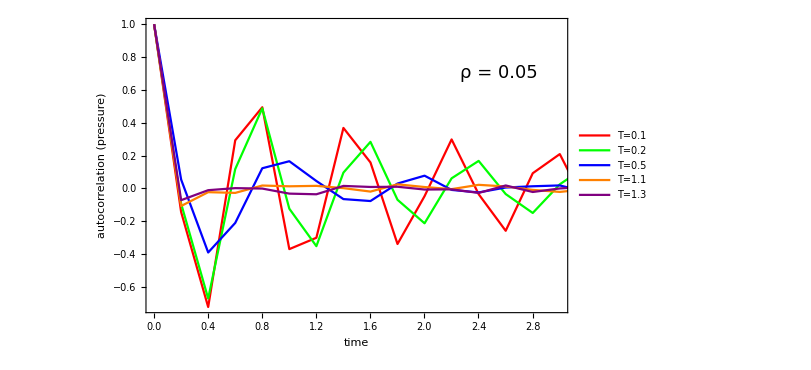

```mathematica
pl=ListLinePlot[{
cor1,
cor2, cor3, cor4, cor5
}, PlotRange->{{0,3}, All}, DataRange->{0, 0.2*Length[cor1]}, 
Frame->True, ImageSize->600,FrameLabel->{Style["time",20], Style["autocorrelation (pressure)",20]},FrameTicksStyle->14,PlotStyle->{Red,Green,Blue,Orange, RGBColor[{0.5,0,0.5}], Brown, Black},AxesOrigin->{0,0},
Epilog->{Inset[LineLegend[{Red,Green,Blue,Orange, RGBColor[{0.5,0,0.5}], Brown, Black},{"T=0.1", "T=0.2", "T=0.5", "T=1.1","T=1.3" }, LabelStyle->18, LegendLayout->{"Row",1}],{1.5,0.9}],
Inset[Style["ρ = 0.05", 18],{2.55,0.7}]
}]
```

```mathematica
Export["/home/jure/Documents/molecular_simulation/images_md/autocorrelation_pressure_small_density.png", pl]
```

/home/jure/Documents/molecular_simulation/images_md/autocorrelation_pressure_small_density.png

```mathematica
datap1=getDatap[0.15,0.9,0.4,100];
datap2=getDatap[0.2,0.9,0.4,100];
datap3=getDatap[0.5,0.9,0.4,100];
datap4=getDatap[1.1,0.9,0.4,100];
datap5=getDatap[1.3,0.9,0.4,100];
cor1=Table[CorrelationFunction[datap1, i],{i,0,(datap1//Length)-1}];
cor2=Table[CorrelationFunction[datap2, i],{i,0,(datap2//Length)-1}];
cor3=Table[CorrelationFunction[datap3, i],{i,0,(datap3//Length)-1}];
cor4=Table[CorrelationFunction[datap4, i],{i,0,(datap4//Length)-1}];
cor5=Table[CorrelationFunction[datap5, i],{i,0,(datap5//Length)-1}];
```

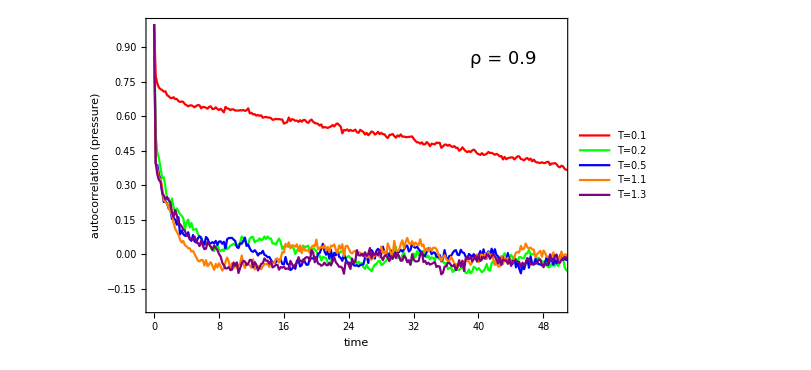

```mathematica
pl=ListLinePlot[{
cor1,
cor2, cor3, cor4, cor5
}, PlotRange->{{0,50}, All}, DataRange->{0, 0.2*Length[cor1]}, 
Frame->True, ImageSize->600,FrameLabel->{Style["time",20], Style["autocorrelation (pressure)",20]},FrameTicksStyle->14,PlotStyle->{Red,Green,Blue,Orange, RGBColor[{0.5,0,0.5}], Brown, Black},AxesOrigin->{0,0},
Epilog->{Inset[LineLegend[{Red,Green,Blue,Orange, RGBColor[{0.5,0,0.5}], Brown, Black},{"T=0.1", "T=0.2", "T=0.5", "T=1.1","T=1.3" }, LabelStyle->18, LegendLayout->{"Row",1}],{25,0.95}],
Inset[Style["ρ = 0.9", 18],{43,0.85}]
}]
```

```mathematica
Export["/home/jure/Documents/molecular_simulation/images_md/autocorrelation_pressure_high_density.png", pl]
```

/home/jure/Documents/molecular_simulation/images_md/autocorrelation_pressure_high_density.png

```mathematica
Estimatesigma2[data_]:=Block[{sigma2, factor=1.0},
sigma2=Variance[data];
sigma2=sigma2*(1+Sum[(1-i/Length[data])*CorrelationFunction[data,i],{i,1,Length[data]-1}]);
Return[Around[ data//Mean,sigma2//Sqrt]]
]
```

```mathematica
Estimatesigma2[getDatap[0.1,0.85,0.4,100]]
```

-4.250.11

```mathematica
data100=Import["/home/jure/Documents/molecular_simulation/md_data_energy_pressure/averages_gamma0.40_num_particles200.dat"];
```

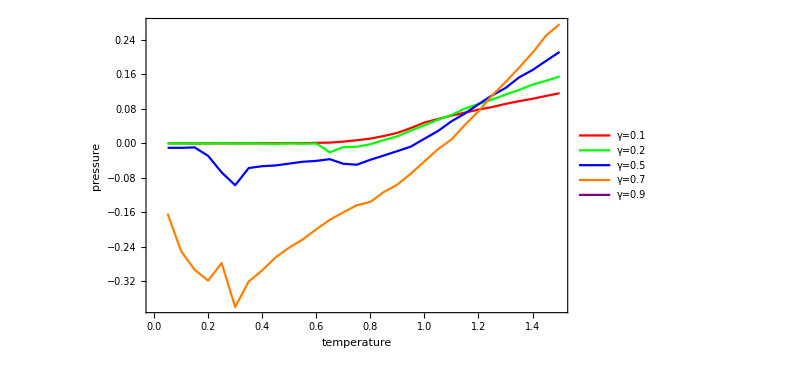

```mathematica
ListLinePlot[{
SortBy[Select[data100, #[[2]]==0.1&][[All, {1,5}]],First],
SortBy[Select[data100, #[[2]]==0.15&][[All, {1,5}]], First],
SortBy[Select[data100, #[[2]]==0.25&][[All, {1,5}]], First],
SortBy[Select[data, #[[2]]==0.35&][[All, {1,5}]], First]
},
PlotRange->All, Frame->True, ImageSize->600,FrameLabel->{Style["temperature",20], Style["pressure",20]},FrameTicksStyle->14,PlotStyle->{Red,Green,Blue,Orange, RGBColor[{0.5,0,0.5}], Brown, Black},AxesOrigin->{0,0},
Epilog->{Inset[LineLegend[{Red,Green,Blue,Orange, RGBColor[{0.5,0,0.5}], Brown, Black},{"γ=0.1", "γ=0.2", "γ=0.5", "γ=0.7","γ=0.9" }, LabelStyle->18, LegendLayout->{"Row",2}],{65,600}],
Inset[Style["T = 0.85", 18],{62,-312}]
}
]
```

```mathematica
p21=ParallelTable[{density,Estimatesigma2[getDatap[0.45,density,0.4,50]] },{density, 0.05, 1.45, 0.05}];
p41=ParallelTable[{density,Estimatesigma2[getDatap[0.9,density,0.4,50]] },{density, 0.05, 1.45, 0.05}];
p51=ParallelTable[{density,Estimatesigma2[getDatap[1.1,density,0.4,50]] },{density, 0.05, 1.45, 0.05}];

p22=ParallelTable[{density,Estimatesigma2[getDatap[0.45,density,0.4,100]] },{density, 0.05, 1.45, 0.05}];
p42=ParallelTable[{density,Estimatesigma2[getDatap[0.9,density,0.4,100]] },{density, 0.05, 1.45, 0.05}];
p52=ParallelTable[{density,Estimatesigma2[getDatap[1.1,density,0.4,100]] },{density, 0.05, 1.45, 0.05}];

p23=ParallelTable[{density,Estimatesigma2[getDatap[0.45,density,0.4,200]] },{density, 0.05, 1.45, 0.05}];
p43=ParallelTable[{density,Estimatesigma2[getDatap[0.9,density,0.4,200]] },{density, 0.05, 1.45, 0.05}];
p53=ParallelTable[{density,Estimatesigma2[getDatap[1.1,density,0.4,200]] },{density, 0.05, 1.45, 0.05}];

p24=ParallelTable[{density,Estimatesigma2[getDatap[0.45,density,0.4,500]] },{density, 0.05, 1.45, 0.05}];
p44=ParallelTable[{density,Estimatesigma2[getDatap[0.9,density,0.4,500]] },{density, 0.05, 1.45, 0.05}];
p54=ParallelTable[{density,Estimatesigma2[getDatap[1.1,density,0.4,500]] },{density, 0.05, 1.45, 0.05}];
```

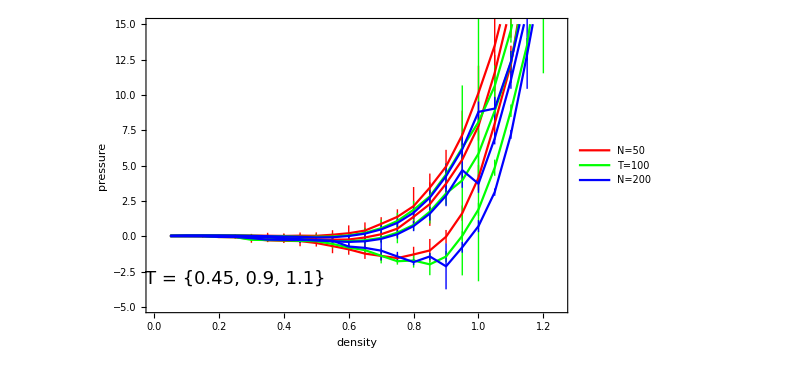

```mathematica
pl=ListLinePlot[{
p21, p41, p51, p22,p42,p52,p23,p43,p53
},
PlotRange->{{0,1.25},{-5,15}}, Frame->True, ImageSize->600,FrameLabel->{Style["density",20], Style["pressure",20]},FrameTicksStyle->14,PlotStyle->{Red,Red,Red,Green,Green,Green,Blue,Blue,Blue, Black, Black, Black},AxesOrigin->{0,0},
Epilog->{Inset[LineLegend[{Red,Green,Blue},{"N=50", "T=100", "N=200", "T=0.9","T=1.1", "T=1.3" }, LabelStyle->18, LegendLayout->{"Row",1}],{0.4,14}],
Inset[Style["T = {0.45, 0.9, 1.1} ", 18],{0.25,-3}],
Inset[ListLinePlot[{
p21, p41, p51, p22,p42,p52,p23,p43,p53
}, PlotRange->{{0.4,1.05},{-3,2}}, Frame->True, ImageSize->280,FrameTicksStyle->14,PlotStyle->{Red,Red,Red,Green,Green,Green,Blue,Blue,Blue, Black, Black, Black},AxesOrigin->{0,0}]
,{0.35, 7}]
}
]
```

```mathematica
Export["/home/jure/Documents/molecular_simulation/images_md/pressure_density_variousT_var_NumParticles.png", pl];
```

```mathematica
SetDirectory[NotebookDirectory[]];
getDatae[t_,density_,gamma_,n_ ]:=Block[{data, filename, error, potential, kinetic},
filename=StringJoin[{"md_data_energy_pressure/energy_density",ToString[NumberForm[density*1.0,{3,2}]], 
"_temperature",ToString[NumberForm[t*1.0,{3,2}]],"_gamma",ToString[NumberForm[gamma*1.0,{3,2}]], "_num_particles", ToString[n], ".dat"}];
data=Import[filename];
Return[Total/@data];
]
```

```mathematica
getDatak[t_,density_,gamma_,n_ ]:=Block[{data, filename, error, potential, kinetic},
filename=StringJoin[{"md_data_energy_pressure/energy_density",ToString[NumberForm[density*1.0,{3,2}]], 
"_temperature",ToString[NumberForm[t*1.0,{3,2}]],"_gamma",ToString[NumberForm[gamma*1.0,{3,2}]], "_num_particles", ToString[n], ".dat"}];
data=Import[filename];
Return[data[[All,2]]];
]
```

```mathematica
datak1=getDatak[0.1,0.05,0.4,100];
datak2=getDatak[0.2,0.05,0.4,100];
datak3=getDatak[0.5,0.05,0.4,100];
datak4=getDatak[1.1,0.05,0.4,100];
datak5=getDatak[1.3,0.05,0.4,100];
cor1=Table[CorrelationFunction[datak1, i],{i,0,(datak1//Length)-1}];
cor2=Table[CorrelationFunction[datak2, i],{i,0,(datak2//Length)-1}];
cor3=Table[CorrelationFunction[datak3, i],{i,0,(datak3//Length)-1}];
cor4=Table[CorrelationFunction[datak4, i],{i,0,(datak4//Length)-1}];
cor5=Table[CorrelationFunction[datak5, i],{i,0,(datak5//Length)-1}];
```

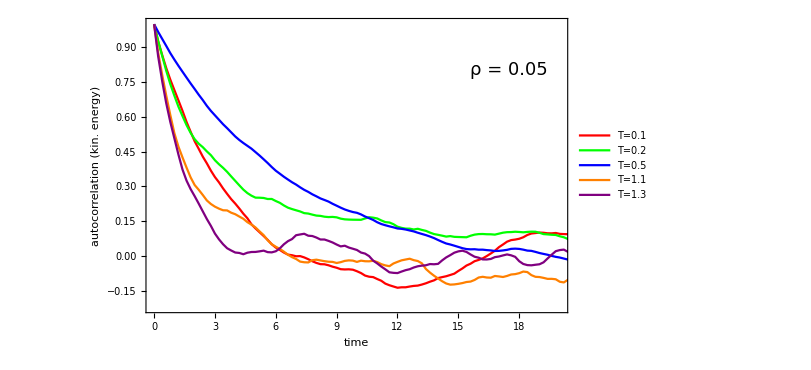

```mathematica
pl=ListLinePlot[{
cor1,
cor2, cor3, cor4, cor5
}, PlotRange->{{0,20}, All}, DataRange->{0, 0.2*Length[cor1]}, 
Frame->True, ImageSize->600,FrameLabel->{Style["time",20], Style["autocorrelation (kin. energy)",20]},FrameTicksStyle->14,PlotStyle->{Red,Green,Blue,Orange, RGBColor[{0.5,0,0.5}], Brown, Black},AxesOrigin->{0,0},
Epilog->{Inset[LineLegend[{Red,Green,Blue,Orange, RGBColor[{0.5,0,0.5}], Brown, Black},{"T=0.1", "T=0.2", "T=0.5", "T=1.1","T=1.3" }, LabelStyle->18, LegendLayout->{"Row",1}],{10.5,0.9}],
Inset[Style["ρ = 0.05", 18],{17.5,0.8}]
}]
```

```mathematica
Export["/home/jure/Documents/molecular_simulation/images_md/autocorrelation_kin_energy_small_density.png", pl];
```

```mathematica
datak1=getDatat[0.1,0.9,0.4,100];
datak2=getDatak[0.2,0.9,0.4,100];
datak3=getDatak[0.5,0.9,0.4,100];
datak4=getDatak[1.1,0.9,0.4,100];
datak5=getDatak[1.3,0.9,0.4,100];
cor1=Table[CorrelationFunction[datak1, i],{i,0,(datak1//Length)-1}];
cor2=Table[CorrelationFunction[datak2, i],{i,0,(datak2//Length)-1}];
cor3=Table[CorrelationFunction[datak3, i],{i,0,(datak3//Length)-1}];
cor4=Table[CorrelationFunction[datak4, i],{i,0,(datak4//Length)-1}];
cor5=Table[CorrelationFunction[datak5, i],{i,0,(datak5//Length)-1}];
```

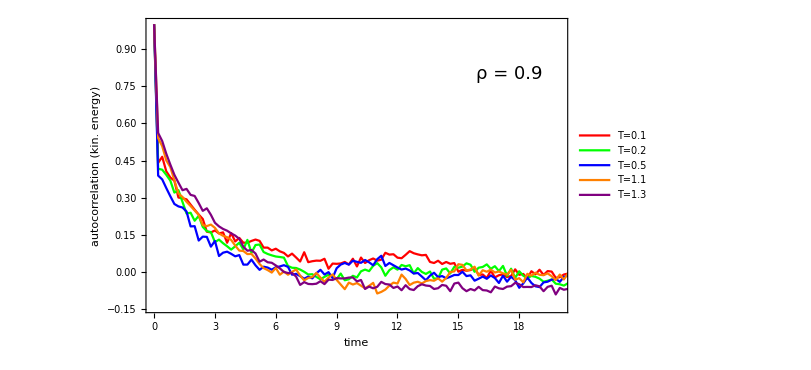

```mathematica
pl=ListLinePlot[{
cor1,
cor2, cor3, cor4, cor5
}, PlotRange->{{0,20}, All}, DataRange->{0, 0.2*Length[cor1]}, 
Frame->True, ImageSize->600,FrameLabel->{Style["time",20], Style["autocorrelation (kin. energy)",20]},FrameTicksStyle->14,PlotStyle->{Red,Green,Blue,Orange, RGBColor[{0.5,0,0.5}], Brown, Black},AxesOrigin->{0,0},
Epilog->{Inset[LineLegend[{Red,Green,Blue,Orange, RGBColor[{0.5,0,0.5}], Brown, Black},{"T=0.1", "T=0.2", "T=0.5", "T=1.1","T=1.3" }, LabelStyle->18, LegendLayout->{"Row",1}],{10.5,0.9}],
Inset[Style["ρ = 0.9", 18],{17.5,0.8}]
}]
```

```mathematica
Export["/home/jure/Documents/molecular_simulation/images_md/autocorrelation_kin_energy_high_density.png", pl];
```

```mathematica
k11=ParallelTable[{temp,Estimatesigma2[getDatak[temp,0.45,0.4,50]] },{temp, 0.05, 1.45, 0.05}];
k21=ParallelTable[{temp,Estimatesigma2[getDatak[temp,0.9,0.4,50]] },{temp, 0.05, 1.45, 0.05}];
k31=ParallelTable[{temp,Estimatesigma2[getDatak[temp,1.1,0.4,50]] },{temp, 0.05, 1.45, 0.05}];
k12=ParallelTable[{temp,Estimatesigma2[getDatak[temp,0.45,0.4,100]] },{temp, 0.05, 1.45, 0.05}];
k22=ParallelTable[{temp,Estimatesigma2[getDatak[temp,0.9,0.4,100]] },{temp, 0.05, 1.45, 0.05}];
k32=ParallelTable[{temp,Estimatesigma2[getDatak[temp,1.1,0.4,100]] },{temp, 0.05, 1.45, 0.05}];
k13=ParallelTable[{temp,Estimatesigma2[getDatak[temp,0.45,0.4,200]] },{temp, 0.05, 1.45, 0.05}];
k23=ParallelTable[{temp,Estimatesigma2[getDatak[temp,0.9,0.4,200]] },{temp, 0.05, 1.45, 0.05}];
k33=ParallelTable[{temp,Estimatesigma2[getDatak[temp,1.1,0.4,200]] },{temp, 0.05, 1.45, 0.05}];
```

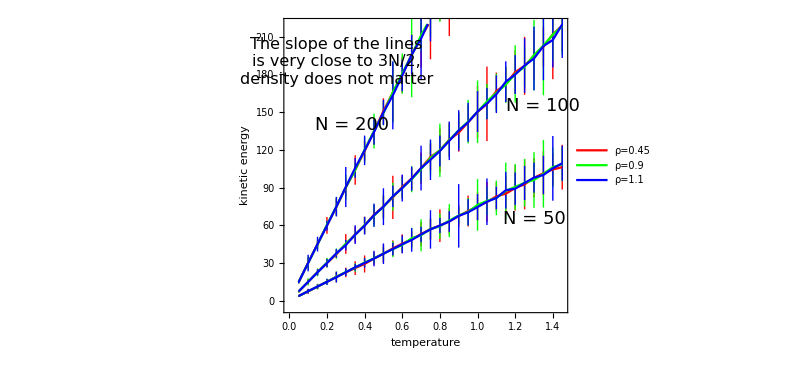

```mathematica
pl=ListLinePlot[{
k11,k21,k31,k12,k22,k32,k13,k23,k33
},
PlotRange->{-5,220}, Frame->True, ImageSize->600,FrameLabel->{Style["temperature",20], Style["kinetic energy",20]},FrameTicksStyle->14,PlotStyle->{Red,Green,Blue},AxesOrigin->{0,0},
Epilog->{Inset[LineLegend[{Red,Green,Blue,Orange, RGBColor[{0.5,0,0.5}], Brown, Black},{"ρ=0.45", "ρ=0.9", "ρ=1.1"}, LabelStyle->18, LegendLayout->{"Row",1}],{1.0,15}],
Inset[Style["N = 50", 18],{1.3,65}],
Inset[Style["N = 100", 18],{1.35,155}],
Inset[Style["N = 200", 18],{0.335,140}],
Inset[Style["The slope of the lines\nis very close to 3N/2,\ndensity does not matter", 16],{0.25,190}]
}
]
```

```mathematica
Export["/home/jure/Documents/molecular_simulation/images_md/kin_energy_density_variousT_var_NumParticles.png", pl];
```

```mathematica
m1=ParallelTable[{temp,getDatak[temp,0.25,0.4,100] //Mean},{temp, 0.05, 1.45, 0.05}];
m2=ParallelTable[{temp,getDatak[temp,0.45,0.4,100]//Mean },{temp, 0.05, 1.45, 0.05}];
m3=ParallelTable[{temp,getDatak[temp,0.65,0.4,100] //Mean},{temp, 0.05, 1.45, 0.05}];
m4=ParallelTable[{temp,getDatak[temp,0.9,0.4,100]//Mean },{temp, 0.05, 1.45, 0.05}];
m5=ParallelTable[{temp,getDatak[temp,1.1,0.4,100]//Mean},{temp, 0.05, 1.45, 0.05}];
```

```mathematica
LinearModelFit[ m1,x,x]
```

FittedModel[-0.1097+150.203 x]

```mathematica
getDatapot[t_,density_,gamma_,n_ ]:=Block[{data, filename, error, potential, kinetic},
filename=StringJoin[{"md_data_energy_pressure/energy_density",ToString[NumberForm[density*1.0,{3,2}]], 
"_temperature",ToString[NumberForm[t*1.0,{3,2}]],"_gamma",ToString[NumberForm[gamma*1.0,{3,2}]], "_num_particles", ToString[n], ".dat"}];
data=Import[filename];
Return[data[[All,1]]];
]
```

```mathematica
datak1=getDatapot[0.1,0.05,0.4,100];
datak2=getDatapot[0.2,0.05,0.4,100];
datak3=getDatapot[0.5,0.05,0.4,100];
datak4=getDatapot[1.1,0.05,0.4,100];
datak5=getDatapot[1.3,0.05,0.4,100];
cor1=Table[CorrelationFunction[datak1, i],{i,0,(datak1//Length)-1}];
cor2=Table[CorrelationFunction[datak2, i],{i,0,(datak2//Length)-1}];
cor3=Table[CorrelationFunction[datak3, i],{i,0,(datak3//Length)-1}];
cor4=Table[CorrelationFunction[datak4, i],{i,0,(datak4//Length)-1}];
cor5=Table[CorrelationFunction[datak5, i],{i,0,(datak5//Length)-1}];
```

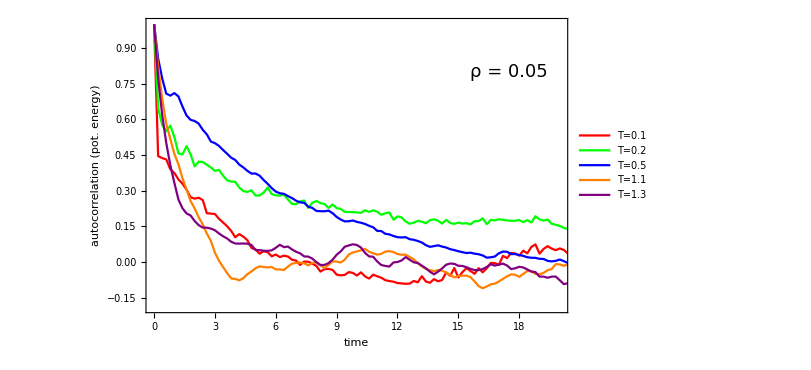

```mathematica
pl=ListLinePlot[{
cor1,
cor2, cor3, cor4, cor5
}, PlotRange->{{0,20}, All}, DataRange->{0, 0.2*Length[cor1]}, 
Frame->True, ImageSize->600,FrameLabel->{Style["time",20], Style["autocorrelation (pot. energy)",20]},FrameTicksStyle->14,PlotStyle->{Red,Green,Blue,Orange, RGBColor[{0.5,0,0.5}], Brown, Black},AxesOrigin->{0,0},
Epilog->{Inset[LineLegend[{Red,Green,Blue,Orange, RGBColor[{0.5,0,0.5}], Brown, Black},{"T=0.1", "T=0.2", "T=0.5", "T=1.1","T=1.3" }, LabelStyle->18, LegendLayout->{"Row",1}],{10.5,0.9}],
Inset[Style["ρ = 0.05", 18],{17.5,0.8}]
}]
```

```mathematica
Export["/home/jure/Documents/molecular_simulation/images_md/autocorrelation_pot_energy_small_density.png", pl];
```

```mathematica
datak1=getDatapot[0.1,0.9,0.4,100];
datak2=getDatapot[0.2,0.9,0.4,100];
datak3=getDatapot[0.5,0.9,0.4,100];
datak4=getDatapot[1.1,0.9,0.4,100];
datak5=getDatapot[1.3,0.9,0.4,100];
cor1=Table[CorrelationFunction[datak1, i],{i,0,(datak1//Length)-1}];
cor2=Table[CorrelationFunction[datak2, i],{i,0,(datak2//Length)-1}];
cor3=Table[CorrelationFunction[datak3, i],{i,0,(datak3//Length)-1}];
cor4=Table[CorrelationFunction[datak4, i],{i,0,(datak4//Length)-1}];
cor5=Table[CorrelationFunction[datak5, i],{i,0,(datak5//Length)-1}];
```

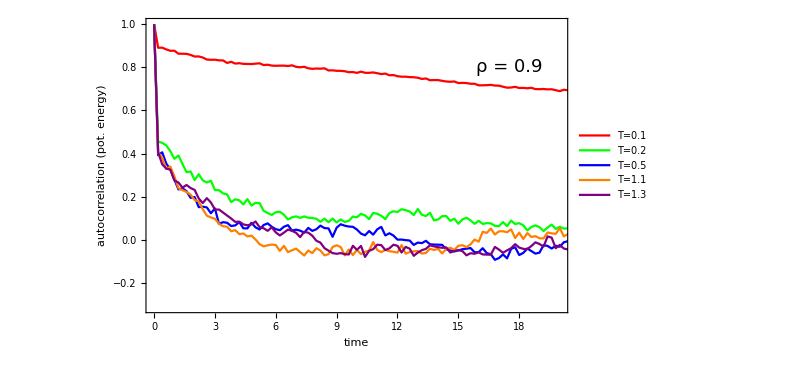

```mathematica
pl=ListLinePlot[{
cor1,
cor2, cor3, cor4, cor5
}, PlotRange->{{0,20}, All}, DataRange->{0, 0.2*Length[cor1]}, 
Frame->True, ImageSize->600,FrameLabel->{Style["time",20], Style["autocorrelation (pot. energy)",20]},FrameTicksStyle->14,PlotStyle->{Red,Green,Blue,Orange, RGBColor[{0.5,0,0.5}], Brown, Black},AxesOrigin->{0,0},
Epilog->{Inset[LineLegend[{Red,Green,Blue,Orange, RGBColor[{0.5,0,0.5}], Brown, Black},{"T=0.1", "T=0.2", "T=0.5", "T=1.1","T=1.3" }, LabelStyle->18, LegendLayout->{"Row",1}],{10.5,0.9}],
Inset[Style["ρ = 0.9", 18],{17.5,0.8}]
}]
```

```mathematica
Export["/home/jure/Documents/molecular_simulation/images_md/autocorrelation_pot_energy_high_density.png", pl];
```

```mathematica
getDatapot[t_,density_,gamma_,n_ ]:=Block[{data, filename, error, potential, kinetic},
filename=StringJoin[{"md_data_energy_pressure/energy_density",ToString[NumberForm[density*1.0,{3,2}]], 
"_temperature",ToString[NumberForm[t*1.0,{3,2}]],"_gamma",ToString[NumberForm[gamma*1.0,{3,2}]], "_num_particles", ToString[n], ".dat"}];
data=Import[filename];
Return[data[[All,1]]/n];
]
```

```mathematica
v11=ParallelTable[{temp,Estimatesigma2[getDatapot[temp,0.45,0.4,50]] },{temp, 0.05, 1.45, 0.05}];
v21=ParallelTable[{temp,Estimatesigma2[getDatapot[temp,0.9,0.4,50]] },{temp, 0.05, 1.45, 0.05}];
v31=ParallelTable[{temp,Estimatesigma2[getDatapot[temp,1.1,0.4,50]] },{temp, 0.05, 1.45, 0.05}];
v12=ParallelTable[{temp,Estimatesigma2[getDatapot[temp,0.45,0.4,100]] },{temp, 0.05, 1.45, 0.05}];
v22=ParallelTable[{temp,Estimatesigma2[getDatapot[temp,0.9,0.4,100]] },{temp, 0.05, 1.45, 0.05}];
v32=ParallelTable[{temp,Estimatesigma2[getDatapot[temp,1.1,0.4,100]] },{temp, 0.05, 1.45, 0.05}];
v13=ParallelTable[{temp,Estimatesigma2[getDatapot[temp,0.45,0.4,200]] },{temp, 0.05, 1.45, 0.05}];
v23=ParallelTable[{temp,Estimatesigma2[getDatapot[temp,0.9,0.4,200]] },{temp, 0.05, 1.45, 0.05}];
v33=ParallelTable[{temp,Estimatesigma2[getDatapot[temp,1.1,0.4,200]] },{temp, 0.05, 1.45, 0.05}];
```

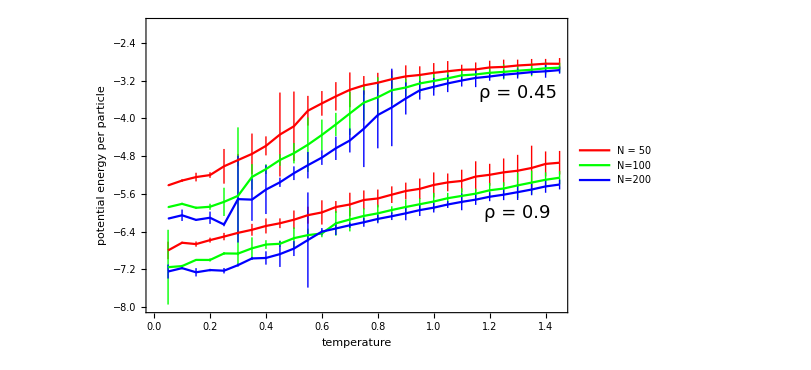

```mathematica
pl=ListLinePlot[{
v11,v21,v12,v22,v13,v23
},
PlotRange->{-8,-2}, Frame->True, ImageSize->600,FrameLabel->{Style["temperature",20], Style["potential energy per particle",20]},FrameTicksStyle->14,PlotStyle->{Red,Red,Green,Green,Blue,Blue, Black, Black, Black},AxesOrigin->{0,0},
Epilog->{Inset[LineLegend[{Red,Green,Blue},{"N = 50", "N=100", "N=200", "ρ=0.9","ρ=1.1" , "ρ=1.4" }, LabelStyle->18, LegendLayout->{"Row",2}],{0.25,-3}],
Inset[Style["ρ = 0.45", 18],{1.3,-3.45}],
Inset[Style["ρ = 0.9", 18],{1.3,-6}],
Inset[Style["The slope of the line is almost exactly 3/2", 18],{62,-312}]
}
]
```

```mathematica
v1=ParallelTable[{n,Estimatesigma2[getDatapot[0.05,0.05,0.4,n]] },{n, {50,80,100,120,150,180,210,250,275,300,500}}];
v2=ParallelTable[{n,Estimatesigma2[getDatapot[0.9,0.45,0.4,n]] },{n, {50,80,100,120,150,180,210,250,275,300,500}}];
v3=ParallelTable[{n,Estimatesigma2[getDatapot[0.9,0.9,0.4,n]] },{n, {50,80,100,120,150,180,210,250,275,300,500}}];
v4=ParallelTable[{n,Estimatesigma2[getDatapot[1.3,0.45,0.4,n]] },{n, {50,80,100,120,150,180,210,250,275,300,500}}];
```

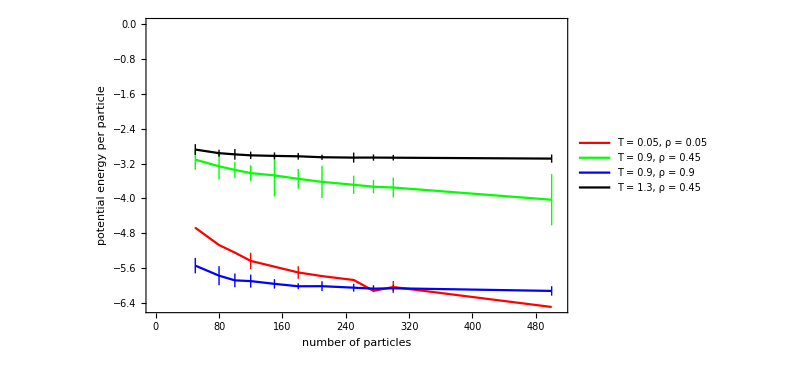

```mathematica
pl=ListLinePlot[{
v1,v2,v3, v4
},
PlotRange->{{-2,510}, All}, Frame->True, ImageSize->600,FrameLabel->{Style["number of particles",20], Style["potential energy per particle",20]},FrameTicksStyle->14,PlotStyle->{Red,Green,Blue, Black},AxesOrigin->{0,0},
Epilog->{Inset[LineLegend[{Red,Green,Blue, Black},{"T = 0.05, ρ = 0.05", "T = 0.9, ρ = 0.45", "T = 0.9, ρ = 0.9", "T = 1.3, ρ = 0.45", "ρ=0.9","ρ=1.1" , "ρ=1.4" }, LabelStyle->18, LegendLayout->{"Row",2}],{250,-1}],
Inset[Style["ρ = 0.05, T = ", 18],{1.3,-300.45}],
Inset[Style["ρ = 0.9, T = ", 18],{1.3,-600}],
Inset[Style["The slope of the line is almost exactly 3/2", 18],{62,-312}]
}
]
```

```mathematica
Export["/home/jure/Documents/molecular_simulation/images_md/pot_energy_density_var_NumPArticles.png", pl];
```

```mathematica
getDatat[t_,density_,gamma_,n_ ]:=Block[{data, filename, error, potential, kinetic},
filename=StringJoin[{"md_data_energy_pressure/energy_density",ToString[NumberForm[density*1.0,{3,2}]], 
"_temperature",ToString[NumberForm[t*1.0,{3,2}]],"_gamma",ToString[NumberForm[gamma*1.0,{3,2}]], "_num_particles", ToString[n], ".dat"}];
data=Import[filename];
Return[data[[All,1]]+ data[[All,2]]];
]
```

```mathematica
sigma2[data_]:=Block[{sigma2, factor=1.0},
sigma2=Variance[data];
sigma2=sigma2*(1+Sum[(1-i/Length[data])*CorrelationFunction[data,i],{i,1,Length[data]-1}]);
Return[Around[sigma2]]
]
```

```mathematica
cv1=ParallelTable[{temp,sigma2[getDatapot[temp,0.25,0.4,100]]/temp^2 },{temp, 0.05, 1.45, 0.05}];
cv2=ParallelTable[{temp,sigma2[getDatapot[temp,0.45,0.4,100]]/temp^2 },{temp, 0.05, 1.45, 0.05}];
cv3=ParallelTable[{temp,sigma2[getDatapot[temp,0.65,0.4,100]]/temp^2},{temp, 0.05, 1.45, 0.05}];
cv4=ParallelTable[{temp,sigma2[getDatapot[temp,0.9,0.4,100]]/temp^2 },{temp, 0.05, 1.45, 0.05}];
cv5=ParallelTable[{temp,sigma2[getDatapot[temp,1.1,0.4,100]]/temp^2 },{temp, 0.05, 1.45, 0.05}];
cv6=ParallelTable[{temp,sigma2[getDatapot[temp,1.4,0.4,100]]/temp^2},{temp, 0.05, 1.45, 0.05}];
```

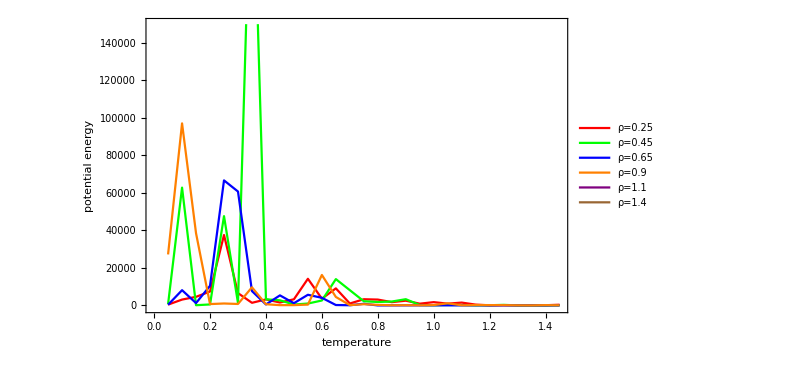

```mathematica
pl=ListLinePlot[{
cv1, cv2, cv3, cv4
},
PlotRange->{-800,150020}, Frame->True, ImageSize->600,FrameLabel->{Style["temperature",20], Style["potential energy",20]},FrameTicksStyle->14,PlotStyle->{Red,Green,Blue,Orange, RGBColor[{0.5,0,0.5}], Brown, Black},AxesOrigin->{0,0},
Epilog->{Inset[LineLegend[{Red,Green,Blue,Orange, RGBColor[{0.5,0,0.5}], Brown, Black},{"ρ=0.25", "ρ=0.45", "ρ=0.65", "ρ=0.9","ρ=1.1" , "ρ=1.4" }, LabelStyle->18, LegendLayout->{"Row",2}],{0.42,90}],
Inset[Style["T = 0.85", 18],{62,-312}],
Inset[Style["The slope of the line is almost exactly 3/2", 18],{62,-312}]
}
]
```